Get["CoxeterGroups`CoxeterVisualisation`"];

|  | "" |  | "»"

|  | "" | "" |

### Euclidean geometry

```mathematica
EuclideanPoints[{{1},{2},{3}}]
Graphics[%]
```

Point[{{1,0},{2,0},{3,0}}]

-Graphics-

```mathematica
EuclideanReflection[{{5}},{1}]
```

{9}

```mathematica
EuclideanLineSegments[{{1},{2},{3}}]
```

-Graphics-

```mathematica
EuclideanPolygon[{{0,0},{1,0},{1,1},{0,1}},Red]
```

-Graphics-

```mathematica
NormalVector[{{0,0},{1,0}}]
```

{0,-1}

```mathematica
EuclideanReflection[{{0,0},{1,0}},{1,1}]
```

{1,-1}

```mathematica
NormalVector[{{1,0,0},{0,1,0},{0,0,0}}]
```

{0,0,1}

```mathematica
EuclideanPolyhedron[{{1,0,0},{0,1,0},{0,0,0},{0,0,1}},Red]
```

-Graphics3D-

```mathematica
Show[
EuclideanPolyhedron[{{1,0,0},{0,1,0},{0,0,0},{0,0,1}},Red],
EuclideanPolyhedron[{{1,0,0},{0,1,0},{1,1,1},{0,0,1}},Red]
]
```

-Graphics3D-

### Spherical geometry

```mathematica
Bearing[{{0,0},{1,1}}]
```

π/4

```mathematica
Bearing[{{1,1,1},{2,3,4}}]
```

-π+ArcTan[(-4/(√3)+1/3 (-3+√3)+1/2 (3+√3))/(-4/(√3)+1/2 (-3+√3)+1/3 (3+√3))]

```mathematica
SphericalArc[{{1,0},{0,-1}},Red]
```

-Graphics-

```mathematica
SphericalReflection[{{1,0}},{0,1}]
```

{0.,-1.}

```mathematica
CircularArc3D[{0,0,0},Normalize[{4,3,2}],Normalize[{1,2,3}]]
```

-Graphics3D-

```mathematica
Circle3D[{0,0,0},Normalize[{4,3,2}],Normalize[{1,2,3}],1,Red,Thin]
```

-Graphics3D-

```mathematica
Circle3D[{0,0,0},{1,2,3}]
```

-Graphics3D-

```mathematica
SphericalPolygon[{{1,0,0},Normalize[{1,1,0}],Normalize[{1,1,1}]},{0,0,0},1,Red]
```

-Graphics3D-

```mathematica
SphericalReflection[{{1,0,0},{0,1,0}},{0,0,1}]
```

{0,0,-1}

### Hyperbolic geometry

### Transformations

ActsOnAPlaneQ[TriangleCG[2,3,4]]

True

|  | "" |  | "»"

|  | "" | "" |

ActsOnAPlaneQ[RAPolygonG[5]]

True

|  | "" |  | "»"

|  | "" | "" |

ActsOnAPlaneQ[RABipartiteG[2,3]]

False

|  | "" |  | "»"

|  | "" | "" |

ChamberVertices[TypeA[3],""]

{{-1/(√6),-1/(√2),1/(√3)},{0,0,1},{-(2 √2)/3,0,1/3}}

|  | "" |  | "»"

|  | "" | "" |

ChamberWalls[TypeA[3]]

{{{-1/(√6),-1/(√2),1/(√3)},{0,0,1}},{{0,0,1},{-(2 √2)/3,0,1/3}},{{-(2 √2)/3,0,1/3},{-1/(√6),-1/(√2),1/(√3)}}}

|  | "" |  | "»"

|  | "" | "" |

WallGeneratorPairs[TypeA[3]]

<|"s1"→{{-1/(√6),-1/(√2),1/(√3)},{0,0,1}},"s2"→{{0,0,1},{-(2 √2)/3,0,1/3}},"s3"→{{-(2 √2)/3,0,1/3},{-1/(√6),-1/(√2),1/(√3)}}|>

|  | "" |  | "»"

|  | "" | "" |

Transformation[TypeA[3],"s3",{0,0,1}]

{-(√2)/3,-√(2/3),-1/3}

|  | "" |  | "»"

|  | "" | "" |

ChamberVertices[TypeBE[2],""]

{{0,0},{1,1},{1,0}}

|  | "" |  | "»"

|  | "" | "" |

ChamberWalls[TypeBE[2]]

{{{0,0},{1,1}},{{1,1},{1,0}},{{1,0},{0,0}}}

|  | "" |  | "»"

|  | "" | "" |

WallGeneratorPairs[TypeBE[2]]

<|"s1"→{{0,0},{1,1}},"s2"→{{1,1},{1,0}},"s3"→{{1,0},{0,0}}|>

|  | "" |  | "»"

|  | "" | "" |

Transformation[TypeBE[2],"s1",{1,0}]

{0,1}

|  | "" |  | "»"

|  | "" | "" |

WallGeneratorPairs[TypeAE[1]]

<|"s1"→{{0}},"s2"→{{1}}|>

|  | "" |  | "»"

|  | "" | "" |

Transformation[TypeAE[1],"s1s2s1s2",{0}]

{-4}

|  | "" |  | "»"

|  | "" | "" |

ChamberVertices[I2[4],""]

{{0,1},{1/(√2),1/(√2)}}

|  | ""

ChamberWalls[I2[4]]

{{{0,1}},{{1/(√2),1/(√2)}}}

|  | ""

WallGeneratorPairs[I2[4]]

<|"s1"→{{0,1}},"s2"→{{1/(√2),1/(√2)}}|>

|  | ""

WallGeneratorPairs[I2[4]][["s1"]]

{{0,1}}

|  | ""

### Chambers

```mathematica
ChamberVertices[H3,""]
```

{{1/2 √(1/2 (3+√5)),1/(√(2 (3+√5))),(1+√5)/(2 √(2 (3+√5)))},{1/(√3),1/(√3),1/(√3)},{(2+√5) √(2/(25+11 √5)),0,(3+√5)/(√(50+22 √5))}}

```mathematica
ChamberVertices[TypeBE[2],"s1s2s3s"]
```

{{0,2},{-1,1},{0,1}}

```mathematica
Chamber[TypeA[3],""]
```

-Graphics3D-

```mathematica
Chamber[TypeBE[2],"",Red]
```

-Graphics-

```mathematica
ChamberVertices[I2[2],""]
```

{{0,1},{1,0}}

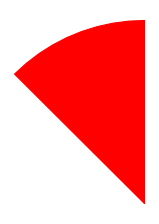

```mathematica
Chamber[I2[4],"s1",Red]
```

```mathematica
Chamber[TypeAE[1],"s1"]
Chamber[TypeAE[1],"s1",
"Outlined"->True,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
Chamber[TypeAE[1],"s1",
"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ChamberBarycentre[TypeA[3],""]
```

{(-(2 √2)/3-1/(√6))/(3 √(1/18+1/9 (4/3+1/(√3))^2+1/9 ((2 √2)/3+1/(√6))^2)),-1/(3 √(2 (1/18+1/9 (4/3+1/(√3))^2+1/9 ((2 √2)/3+1/(√6))^2))),(4/3+1/(√3))/(3 √(1/18+1/9 (4/3+1/(√3))^2+1/9 ((2 √2)/3+1/(√6))^2))}

```mathematica
ShowChambers[TypeA[3],{"","s1","s2","s3","s1s2","s1s2s3"}]
ShowChambers[TypeB[3],{"","s1","s2","s3","s1s2","s1s2s3"},"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
ShowChambers[H3,{"","s2","s3","s3s2","s2s3","s2s3s2","s3s2s3","s2s3s2s3","s3s2s3s2","s2s3s2s3s2"},"Outlined"->True,
"OutlineColour"->Green,
"OutlineThickness"->Thick,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

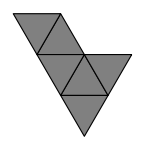

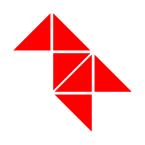

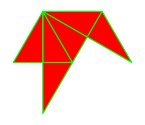

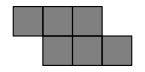

```mathematica
ShowChambers[TypeAE[2],{"","s1","s2","s3","s1s2","s1s2s3"}]
ShowChambers[TypeBE[2],{"","s1","s2","s3","s1s2","s1s2s3"},"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
ShowChambers[GE2,{"","s1","s2","s3","s1s2","s1s2s3"},"Outlined"->True,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
ShowChambers[RAPolygonG[4],{"","s1","s2","s3","s1s2","s1s2s3"}]
```

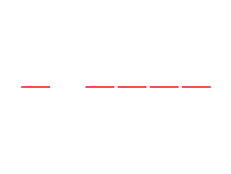

```mathematica
ShowChambers[TypeAE[1],{"","s1","s2","s1s2","s1s2s1s2"},"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
```

```mathematica
ShowChambers[I2[4],{"","s1","s2","s1s2","s1s2s1s2"},"Outlined"->True,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White]
```

-Graphics-

### Hyperplanes

```mathematica
ZeroVector[TypeA[3]]
ZeroVector[TypeAE[2]]
ZeroVector[TypeAE[1]]
ZeroVector[I2[4]]
```

{0,0,0}

{0,0}

{0}

{0,0}

```mathematica
NormalVector[TypeA[3],"s1s2s1"]
NormalVector[TypeAE[2],"s1s2s1"]
NormalVector[I2[4],"s1s2s1"]
```

{0.5,0.866025,0.}

{1.66533×10^-16,1.}

{-1.,0.}

```mathematica
BasePoint[TypeAE[2],"s1s2s1"]
```

{-0.5,0.866025}

```mathematica
BasePoint[TypeBE[2],"s1s2s1"]
```

{2.22045×10^-16,1.}

```mathematica
BasePoint[GE2,"s1s2s1"]
```

{0.75,0.433013}

```mathematica
BasePoint[TypeAE[1],"s1s2s1"]
```

{-1}

```mathematica
CoxeterHyperplane[TypeA[3],"s1s2s1"]
```

-Graphics3D-

```mathematica
CoxeterHyperplane[TypeAE[2],"s1s2s1"]
```

Hyperplane[{1.66533×10^-16,1.},{-0.5,0.866025}]

```mathematica
CoxeterHyperplane[TypeAE[1],"s1s2s1"]
```

Point[{-1,0}]

```mathematica
CoxeterHyperplane[I2[4],"s1s2s1"]
```

Line[{{{-0.707107,0.707107}},{{0.707107,-0.707107}}}]

```mathematica
ShowHyperplanes[TypeA[3],{"s1","s2","s3","s1s2s1"}]
ShowHyperplanes[TypeA[3],{"s1","s2","s3","s1s2s1"},"Colour"->Red,
"Thickness"->Thin,
"PointSize"->Large,
"Opacity"->.2]
```

-Graphics3D-

-Graphics3D-

```mathematica
ShowHyperplanes[TypeAE[2],{"s1","s2","s3","s1s2s1"}]
ShowHyperplanes[TypeAE[2],{"s1","s2","s3","s1s2s1"},"Colour"->Red,
"Thickness"->Thin,
"PointSize"->Large,
"Opacity"->.2]
```

-Graphics-

-Graphics-

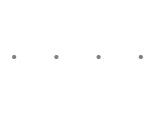

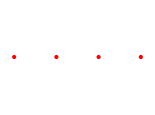

```mathematica
ShowHyperplanes[TypeAE[1],{"s1","s2","s2s1s2","s1s2s1"}]
ShowHyperplanes[TypeAE[1],{"s1","s2","s2s1s2","s1s2s1"},"Colour"->Red,
"Thickness"->Thin,
"PointSize"->Large,
"Opacity"->.2]
```

```mathematica
ShowHyperplanes[I2[7],{"s1","s2","s2s1s2","s1s2s1"}]
ShowHyperplanes[I2[7],{"s1","s2","s2s1s2","s1s2s1"},"Colour"->Red,
"Thickness"->Thin,
"PointSize"->Large,
"Opacity"->.2]
```

-Graphics-

-Graphics-

### Galleries

```mathematica
Gallery[TypeA[3],"s1s2s3s1"]
Gallery[TypeA[3],"s1s2s3s1","Colour"-> Green,"Thickness"->Thin,"Vertices"->True,"PointSize"->Large]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[
ShowChambers[TypeA[3],{"","s1","s2","s3","s1s2","s1s2s3"}],
Gallery[TypeA[3],{"s1s2s3s1","s2s3s1s2s1","s2s1s3s1s3","s2s3s2s1s2"},"Colour"-> Green,"Thickness"->Thin,"Vertices"->True,"PointSize"->Large]
]
```

-Graphics3D-

```mathematica
Gallery[TypeAE[2],"s1s2s3s1"]
Gallery[TypeAE[2],"s1s2s3s1","Colour"-> Green,"Thickness"->Thin,"Vertices"->True,"PointSize"->Large]
```

-Graphics-

-Graphics-

```mathematica
VisualisationDimension[TypeAE[1]]
```

1

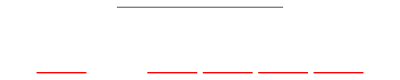

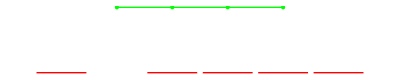

```mathematica
Show[
ShowChambers[TypeAE[1],{"","s1","s2","s1s2","s1s2s1s2"},"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White],
Gallery[TypeAE[1],"s1s2s1"]
]
Show[
ShowChambers[TypeAE[1],{"","s1","s2","s1s2","s1s2s1s2"},"Outlined"->False,
"OutlineColour"->Green,
"OutlineThickness"->Thin,
"PointSize"->Large,
"Colour"->Red,
"Thickness"->Thin,
"Opacity"->1,
"UnderlyingSphere"->False,
"UnderlyingSphereColour"->White],Gallery[TypeAE[1],"s1s2s1","Colour"-> Green,"Thickness"->Thin,"Vertices"->True,"PointSize"->Large]
]
```

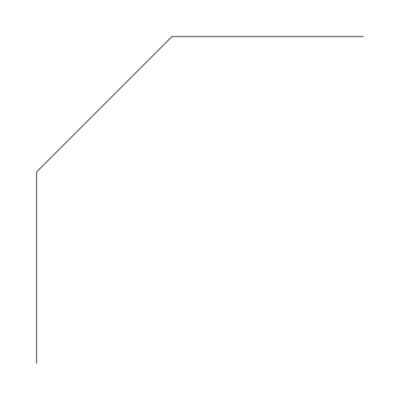

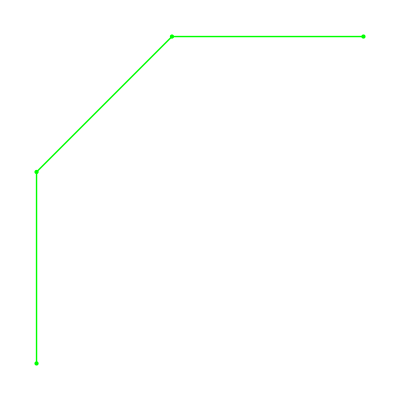

```mathematica
Gallery[I2[4],"s1s2s1"]
Gallery[I2[4],"s1s2s1","Colour"-> Green,"Thickness"->Thin,"Vertices"->True,"PointSize"->Large]
```

### Show Functions

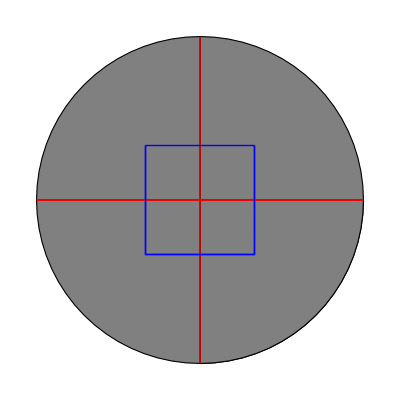

```mathematica
I2[2];
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2"},"Colour"->Blue]
]
```

{{1,5},{5,1}}

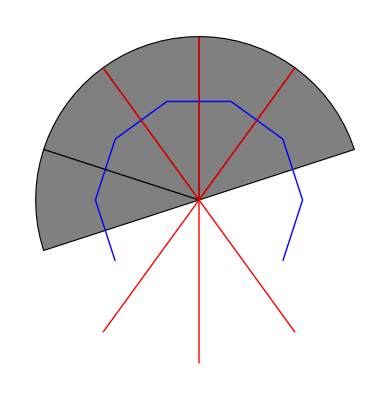

```mathematica
I2[5]
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2"},"Colour"->Blue]
]
```

```mathematica
TypeA[3]
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,3,2},{3,1,3},{2,3,1}}

-Graphics3D-

```mathematica
TypeB[3]
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,3,2},{3,1,4},{2,4,1}}

-Graphics3D-

```mathematica
H3
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,3,2},{3,1,5},{2,5,1}}

-Graphics3D-

{{1,∞},{∞,1}}

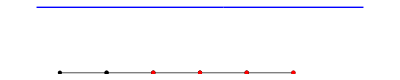

```mathematica
TypeAE[1]
Show[
ShowChambers[TypeAE[1],{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[TypeAE[1],{"s1","s2","s1s2s1","s2s1s2"},"Colour"->Red],
ShowGalleries[TypeAE[1],{"s1s2s1s2","s2s1s2"},"Colour"->Blue]
]
```

```mathematica
TypeAE[2]
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,3,3},{3,1,3},{3,3,1}}

-Graphics-

```mathematica
TypeBE[2]
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,4,2},{4,1,4},{2,4,1}}

-Graphics-

```mathematica
GE2
Show[
ShowChambers[%,{"","s1","s2","s1s2","s1s2s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s1"},"Colour"->Blue]
]
```

{{1,3,2},{3,1,6},{2,6,1}}

-Graphics-

```mathematica
RAPolygonG[4]
Show[
ShowChambers[%,{"","s1","s2","s1s3","s1s4s1"}],
ShowHyperplanes[%,{"s1","s2","s3","s1s2s1"},"Colour"->Red],
ShowGalleries[%,{"s1s2s1s2","s2s1s2","s3s2s4s1"},"Colour"->Blue]
]
```

{{1,2,∞,2},{2,1,2,∞},{∞,2,1,2},{2,∞,2,1}}

-Graphics-

```mathematica
Get["CoxeterGroups`CoxeterVisualisation`"];
```

```mathematica
Get["CoxeterGroups`ElementEnumeration`"]
```

```mathematica
boldred=RGBColor[191/255,4/255,57/255];
boldblue=RGBColor[59/255,199/255,255/255];
boldgreen=RGBColor[0/255,178/255,0/255];
boldorange=RGBColor[229/255,115/255,0/255];
boldpurple=RGBColor[120/255,29/255,145/255];
```

```mathematica
H3chambers=ShowChambers[H3,CoxeterGroupElements[H3,MaxLength[H3]],"Colour"-> boldblue]
```

-Graphics3D-

```mathematica
H3FC=ShowChambers[H3,{""},"Colour"-> Black,"Opacity"->.1];
Show[H3chambers,H3FC]
```

-Graphics3D-

```mathematica
H3galleries=
ShowGalleries[H3,CoxeterGroupElements[H3,MaxLength[H3]],"Colour"->boldpurple]
```

-Graphics3D-

```mathematica
cover=Show[
(*H3chambers,*)
Graphics3D[{boldblue,Opacity[.90],Sphere[{0,0,0},.999]},Boxed->False,ViewPoint->{2,.75,2}],
H3FC,
ShowHyperplanes[H3,Generators[H3],"Colour"->RGBColor[50/255,50/255,214/255]],
H3galleries
]
```

-Graphics3D-

```mathematica
Export["cover.png",cover,ImageResolution->600]
```

cover.png

```mathematica
gens={{"s1","s2","s3"},{"s1","s2s3s2","s3"},{"s1","s2","s3s2s3"},{"s1","s2s3s1s2s1s3s2","s3"},{"s3","s2s3s2","s1s2s3s2s1"}};
```

```mathematica
gentuples=Show[
Graphics3D[{boldblue,Opacity[.90],Sphere[{0,0,0},.999]},Boxed->False,ViewPoint->{1,.75,2}],
H3chambers,
H3FC,
ShowHyperplanes[H3,#,"Colour"->boldred]
]&/@gens
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[
Export["H3"<>ToString[i]<>".png",gentuples[[i]],ImageResolution->600],
{i,1,5}]
```

{H31.png,H32.png,H33.png,H34.png,H35.png}